```mathematica
SDATA={
CI ->  1.5 ,(*MPa*)
TW-> 170, (*mm*)
TL ->  1500 , (*mm*)
(*W->  939.9 9.81 ,N*)
DWR -> 1,
v->2.0 (*m/s*),
IF->0.7 6 3400.0/2(*N*)
};
Wnom =12553.819186375804;(*9.81 939.9*)
Bn = (CI TW TL)/(W (1-Exp[-CI/0.698]))5/(1+6 TW/TL);
DWI = 1 - Abs[(0.7(DWR-1))/(DWR+1)];
GTR = 1.10 (1-Exp[-0.025 Bn])(1-Exp[-17 s])+0.03/DWI;
MRR=2.5/(Bn DWI)+0.03/DWI+(0.5s)/(√Bn);
NTR = GTR - MRR;
TE = NTR/GTR(1-s);
GT = W GTR;
MR = W MRR;
NT = W NTR;
H = GT v/735.5 ;(*cv*)
```

```mathematica
Wnom/9.81
```

1279.7

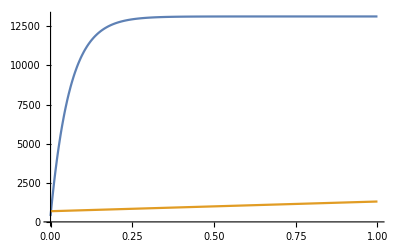

```mathematica
Plot[{GT/.SDATA/.W->Wnom,MR/.SDATA/.W->Wnom},{s,0,1}]
```

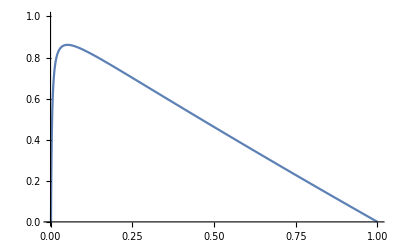

```mathematica
Plot[{TE/.SDATA/.W->Wnom},{s,0,1},PlotRange->{0,1}]
```

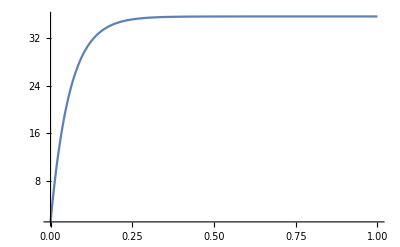

```mathematica
Plot[{H/.SDATA/.W->Wnom},{s,0,1},PlotRange->All]
```

```mathematica
si =s/. FindRoot[D[({TE/.SDATA/.W->Wnom}), s]== 0,{s,0.04}]
```

0.0519585

```mathematica
sol = FindRoot[{D[({TE/.SDATA}), s]== 0,{(NT-IF== 0)/.SDATA}},{{s,si},{W,Wnom+1}}]
```

{s→0.0519585,W→12553.8}

```mathematica
si2=s/.sol⟦1⟧;
Wnom2=W/.sol⟦2⟧;
```

General::munfl: Exp[-62810.4] is too small to represent as a normalized machine number; precision may be lost.

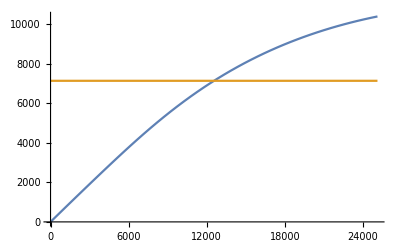

```mathematica
Plot[{NT/.SDATA/.s->si,IF/.SDATA},{W,0,2Wnom}]
```

```mathematica
Bn/.SDATA/.W->Wnom2
```

102.65

```mathematica
GTR/.SDATA/.s-> si/.W->Wnom2
```

0.62567

```mathematica
NTR/.SDATA/.s-> si/.W->Wnom2
```

0.568751

```mathematica
GT/.SDATA/.s-> si/.W->Wnom2
```

7854.55

```mathematica
MR/.SDATA/.s-> si/.W->Wnom2
```

714.548

```mathematica
NT/.SDATA/.s-> si2/.W->Wnom2
```

7140.

```mathematica
TE/.SDATA/.s-> si/.W->Wnom2
```

0.861796

```mathematica
H/.SDATA/.s-> si/.W->Wnom2
```

21.3584